```mathematica
tensorMat[t_]:= {{-((1+3 Cos[2*t])/20),3 Sin[2*t]/(10 Sqrt[2]),-3 Sin[t]^2/10},{3 Sin[2*t]/(10 Sqrt[2]),(1+3 Cos[2*t])/10,(-3 Sin[2*t])/(10 Sqrt[2])},{-3 Sin[t]^2/10,(-3 Sin[2*t])/(10 Sqrt[2]),-((1+3 Cos[2*t])/20)}} 

evals[w_,t_] := Sort[Eigenvalues[(DiagonalMatrix[{-w,0,w}]-IdentityMatrix[3]-tensorMat [t]*(-0.6))]]
```

SetDelayed::write: Tag Plus in ({-4,0}+{-Root[-15.+1. Power[«2»]+Slot[«1»] Plus[«2»]+Power[«2»] Plus[«2»]+7.8 {«3»}[«1»]+3.33067×10^-16 Power[«2»]&,1],-«1»,-Root[«1»&,3]}+Mean[{4,0}+{Root[-15.+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]&,1],Root[-15.+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]&,2],Root[-15.+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]&,3]}])[«1»] is Protected.

$Failed

1000000

1000000+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]

Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]

-1000000+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3]

1/3 (Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

-1000000-Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+1/3 (Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

-Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+1/3 (Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

1000000-Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3]+1/3 (Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-9.4×10^11+0. ⅈ)+1.8×10^11 Cos[2 ang]+5.16306×10^-14 Cos[4 ang]+(-1.×10^12-1.27591×10^-11 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

4

4+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]

Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]

-4+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3]

1/3 (Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

-4-Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+1/3 (Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

-Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+1/3 (Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

4-Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3]+1/3 (Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,1]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,2]+Root[(-14.0867+0. ⅈ)+2.88 Cos[2 ang]-1.73472×10^-18 Cos[4 ang]+(-13.0432+6.93889×10^-18 Cos[2 ang]) #1+3. #1^2+1. #1^3&,3])

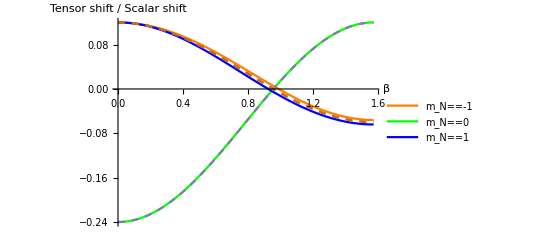

{{1/20 (-1-3 Cos[2 e]),(3 Sin[2 e])/(10 √2),-3/10 Sin[e]^2},{(3 Sin[2 e])/(10 √2),1/10 (1+3 Cos[2 e]),-(3 Sin[2 e])/(10 √2)},{-3/10 Sin[e]^2,-(3 Sin[2 e])/(10 √2),1/20 (-1-3 Cos[2 e])}}

```mathematica
evalsMinusMag[w_,t_]:=evals[w,t]-{-w,0 w}

F[w_,t_]:=-(evalsMinusMag[w,t]-Mean[evalsMinusMag[w,t]])


wl = 1000000

ff1l=(evals[wl,ang][[1]]+wl)
ff2l=(evals[wl,ang][[2]])
ff3l=(evals[wl,ang][[3]]-wl)

meanl=(ff1l+ff2l+ff3l)/3
ff11l=-(ff1l-meanl)
ff22l=-(ff2l-meanl)
ff33l=-(ff3l-meanl)

w = 4

ff1=(evals[w,ang][[1]]+w)
ff2=(evals[w,ang][[2]])
ff3=(evals[w,ang][[3]]-w)

mean=(ff1+ff2+ff3)/3
ff11=-(ff1-mean)
ff22=-(ff2-mean)
ff33=-(ff3-mean)

Plot[{ff11,ff22,ff33, ff11l,ff22l,ff33l},{ang,0,Pi/2}, PlotLegends->{Subscript["m",N]==-1,Subscript["m",N]==0,Subscript["m",N]==1},PlotStyle->{Orange,Green,Blue,Dashed,Dashed,Dashed},AxesLabel->{β,"Tensor shift / Scalar shift"}]
```